# Arclength solutions

#### Fixed radius

```mathematica
(*Solution of the Hamilton equations in dimensionless form as a function of sbB and the shooting variables (for a fixed radial distance):*)
s0B=0;
(*CLOSED*)
SolveShapeEqs[sbB_,pψf0B_,h0B_,FpN_,r0_,αB_,λB_,Lc_,Kb_]:=
Module[{Fcode,pNtoKBTnm,r0B,prfB0},
(*Conversion factor: 1 Subscript[k, B] T/nm is approx 4.142 pN at 300K*)
pNtoKBTnm=1.0/4.142;

(*Non-dimensionalize applied force and the boundary radius*)
Fcode=(FpN*pNtoKBTnm*Lc)/(π*Kb);
r0B=r0/Lc;

(*Evaluate the radiual boundary momentum dynamically to avoid singularities*)
prf0B=If[αB==0,
(*Flat open state limit*)
-pψf0B^2/(4 r0B),
(*Spherical closed state*)
pψf0B*Tan[αB]/r0B-pψf0B^2/(4*r0B*Cos[αB])+(2 r0B)/(Cos[αB] λB^2) (1-Cos[αB])+Fcode Tan[αB]];

NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==αB,(*0,*)
rfB[s0B]==r0B,
hfB[s0B]==h0B,
pψfB[s0B]==pψf0B,
prfB[s0B]==prf0B,
phfB[s0B]==-Fcode
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"StiffnessSwitching"]
]
(*OPEN*)
(*SolveShapeEqs[sbBi_,pψfBi_,h0Bi_,F_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==0,
rfB[s0B]==Sqrt[Ap/π]/Lc,
hfB[s0B]==h0Bi,
pψfB[s0B]==pψfBi,
prfB[s0B]==-pψfBi^2/(4Sqrt[Ap/π]/Lc),
phfB[s0B]==-F
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbBi},Method->"StiffnessSwitching"];*)
(*Solve the Hamilton equations in dimensionless form as a function of the shooting variables, and output the boundary values of ψfB[sB] and rfB[sB] at s = sbB (these are the boundary values used to satisfy the boundary conditions at s = sbB):*)
shoot[sbBi_?NumberQ,pψfBi_?NumberQ,h0Bi_?NumberQ,FpN_?NumberQ,r0_?NumberQ,αB_?NumberQ,λB_?NumberQ,Lc_?NumberQ,Kb_?NumberQ]:=
First[{ψfB[sbBi],rfB[sbBi],hfB[sbBi]}/.SolveShapeEqs[sbBi,pψfBi,h0Bi,FpN,r0,αB,λB,Lc,Kb]];
```

#### Fixed arclength

```mathematica
(*Solution of the Hamilton equations in dimensionless form as a function of sbB and the shooting variables (for a fixed radial distance):*)
s0B=0;
(*CLOSED*)
SolveShapeEqs[prfBi_,pψfBi_,h0Bi_,F_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==αB,(*0,*)
rfB[s0B]==RdomeB Sin[αB],(*Sqrt[Scap/π]/Lc,*)
hfB[s0B]==h0Bi,
pψfB[s0B]==pψfBi,
prfB[s0B]==prfBi,
phfB[s0B]==-F
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"StiffnessSwitching"];
(*OPEN*)
(*SolveShapeEqs[prfBi_,pψfBi_,h0Bi_,F_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==0,
rfB[s0B]==Sqrt[Ap/π]/Lc,
hfB[s0B]==h0Bi,
pψfB[s0B]==pψfBi,
prfB[s0B]==prfBi,
phfB[s0B]==-F
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"StiffnessSwitching"];*)
(*Solve the Hamilton equations in dimensionless form as a function of the shooting variables, and output the boundary values of ψfB[sB] and rfB[sB] at s = sbB (these are the boundary values used to satisfy the boundary conditions at s = sbB):*)
shoot[prfBi_?NumberQ,pψfBi_?NumberQ,h0Bi_?NumberQ,F_?NumberQ]:=First[{ψfB[sbB],prfB[sbB],hfB[sbB]}/.SolveShapeEqs[prfBi,pψfBi,h0Bi,F]];
```

## Plot membrane deformation profile (fixed radius)

β = 4.16334×10^-17 rb = 27. hb = 7.44847×10^-17

pψfBs=-0.976814 sMaxs=1.28614 h0fBs=-0.0776836

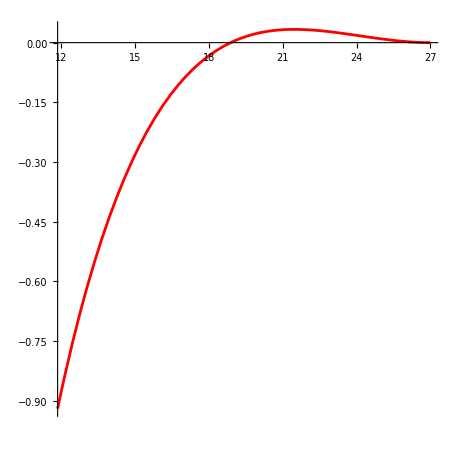

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
r0=Sqrt[Ap/π];
Kb=20;
γ=0.001;
λ=Sqrt[Kb/γ];
Lc=Rdome*Sin[αB];
RdomeB=Rdome/Lc;
λB=λ/Lc;
F=30;
(*sMaxs=3.23715161724963;(*Rp=R0,γ=1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.5546806463488889;
h0fBs=-0.25962859701067303;*)
(*sMaxs=3.748375523602478;(*Rp=Open,γ=0.02 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=2.936739434963147;
h0fBs=-1.750099556432423;*)
pψfBs=1.0067409693543687;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=27nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=1.316426478439671;
h0fBs=-0.2839690963849003;
sols=FindRoot[shoot[sbBi,pψfBi,h0fBi,F,Lc,αB,λB,Lc,Kb]=={0,27/Lc,0},{sbBi,sMaxs},{pψfBi,pψfBs},{h0fBi,h0fBs}];
pψfBs=pψfBi/.sols;
sMaxs=sbBi/.sols;
h0fBs=h0fBi/.sols;
dummy=Evaluate[shoot[sMaxs,pψfBs,h0fBs,F,Lc,αB,λB,Lc,Kb]];
Print["β = ",dummy[[1]]," rb = ",dummy[[2]]*Lc," hb = ",dummy[[3]]];

ndsol=SolveShapeEqs[sMaxs,pψfBs,h0fBs,F,Lc,αB,λB,Lc,Kb];
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
hff[s_]=First[hfB[s]/.ndsol];
Print["pψfBs=",pψfBs," sMaxs=", sMaxs," h0fBs=",h0fBs];
(*en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]]));
G=NIntegrate[en,{s,s0B,sMaxs}];*)
p1=ParametricPlot[{rff[s]*Lc,hff[s]*Lc},{s,s0B,sMaxs},PlotRange->Full,AspectRatio->1,PlotStyle->Red]
```

```mathematica
Print[Rdome*(1-Cos[αB])]
```

1.71254

```mathematica
(*pψfBs=2.4422121303935724;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=40nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=2.678685446564894;
h0fBs=-1.141155221085684;*)
(*pψfBs=1.482768250531759;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=32nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=1.7797003056249288;
h0fBs=-0.48250125033359004;*)
```

```mathematica
(*pψfBs=0.43395472249370337;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=22nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=0.8739774043179569;
h0Bs=-0.15249445368408093;*)
(*pψfBs=-1.0490867636644636;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=17nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=0.44061570277979156;
h0Bs=-0.05859713259588483;*)
(*pψfBs=-0.45296459536455985;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=22nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=0.8668990388039268;
h0Bs=-0.10757550131388502;*)
(*pψfBs=-0.1768616537152269;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=32nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=1.7171783616530936;
h0Bs=-0.18782701259235046;*)
(*pψfBs=-0.09765541955371235;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=42nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=2.565510117931313;
h0Bs=-0.25137246303553124;*)
```

## Finite planar membrane (fixed-r_b)

### Sweep over F

```mathematica
(*Not working for small γ (=0.0001 Subscript[k, B] T/nm^2) with Lc=Rdome Sin[αB] or with Lc=Sqrt[Kb/γ]. Fails at F=-6.8 pN.*)
```

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Kb=20;
γ=0.001;
λ=Sqrt[Kb/γ];
Lc=Rdome*Sin[αB];
(*Lc1=Lc;*)
RdomeB=Rdome/Lc;
λB=λ/Lc;
Clear[fVal];
(*pψfBs=-0.0046466192966983155;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,β=0,rb=200nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=15.91953478362075;
h0fBs=-0.6629937247942063;*)
(*sMaxs=15.89973820626258;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=0,β=0,rb=200nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.31574588266565223;
h0fBs=-0.22770031586868772;*)
(*sMaxs=16.45104859493138;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=200nm,Lc=Rdome Sin[αB]*)
pψfBs=1.6585307275723196;
h0fBs=-3.6650401184224104;*)
(*sMaxs=3.314285503701593;(*Rp=R0,γ=0.2 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0.9270454329774811;
h0fBs=-0.7169956243429715;*)
(*sMaxs=3.2551659575086638;(*Rp=R0,γ=0.5 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0.12474387375436771;
h0fBs=-0.4127626594517183;*)
(*sMaxs=3.248907675437997;(*Rp=R0,γ=0.6 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.045477434376976766;
h0fBs=-0.36641332917668384;*)
(*sMaxs=3.2414105145609646;(*Rp=R0,γ=0.8 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.32547151481174796;
h0fBs=-0.30228375704218424;*)
(*sMaxs=3.23715161724963;(*Rp=R0,γ=1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.5546806463488889;
h0fBs=-0.25962859701067303;*)
(*sMaxs=3.2107534581765758;(*Rp=open,γ=1 Subscript[k, B] T/nm^2,F=0,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0;
h0fBs=0;*)
(*sMaxs=3.2156650567119893;(*Rp=open,γ=1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0.732963636698411;
h0fBs=-0.1654974824476605;*)
(*sMaxs=3.748375523602478;(*Rp=Open,γ=0.02 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=2.936739434963147;
h0fBs=-1.750099556432423;*)
(*pψfBs=N[3.777507724225659,3];(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=40nm,F=-30pN,Lc=R0 Sin[αB]*)
sMaxs=N[3.8527333505950443,3];
h0fBs=N[-2.714453089278311,3];*)
pψfBs=3.2112298744248555;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=42nm,F=-45pN,Lc=R0 Sin[αB]*)
sMaxs=3.261973682180886;
h0fBs=-1.8634576324043182;
(*pψfBs=2.8046799706577676;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=42nm,F=-47.61pN,Lc=R0 Sin[αB]*)
sMaxs=3.0266668652785653;
h0fBs=-1.5054142661251328;*)
Timing[data0=Reap[For[fVal=-45,fVal<=-40,fVal=fVal+0.1,
sols=FindRoot[shoot[sbBi,pψfBi,h0fBi,fVal,Lc,αB,λB,Lc,Kb]=={0,42/Lc,0},{sbBi,sMaxs},{pψfBi,pψfBs},{h0fBi,h0fBs},Method->{"Newton","StepControl"->"LineSearch"},MaxIterations->2000];

pψfBs=pψfBi/.sols;
sMaxs=sbBi/.sols;
h0fBs=h0fBi/.sols;

dummy=Evaluate[shoot[sMaxs,pψfBs,h0fBs,fVal,Lc,αB,λB,Lc,Kb]];
Print["F=",fVal," β=",dummy[[1]]," rf[sbB]=",dummy[[2]]*Lc," hf[sbB]=",dummy[[3]]*Lc];
(*Print["pψfBs=",pψfBs," sMaxs=",sMaxs," h0fBs=",h0fBs];*)

(*Re-run NDSolve with the converged roots to extract the full profile*)
ndsol=SolveShapeEqs[sMaxs,pψfBs,h0fBs,fVal,Lc,αB,λB,Lc,Kb];
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
hff[s_]=First[hfB[s]/.ndsol];

(*Energy Integrand*)
en=Kb π rff[s] ((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2 (1-Cos[ψff[s]]));
Gfootprint=NIntegrate[en,{s,s0B,sMaxs}];
Gtether=-fVal h0fBs Lc;
(*Sow[{fVal,Gfootprint,Gtether}];*)
Sow[{sMaxs,pψfBs,h0fBs}];
]
];
]
data=data0[[2]][[1]];
```

```mathematica
data[[-1]]
```

{3.512,3.44418,-2.19633}

```mathematica
(*pψfBs=3.511998333253313;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=42nm,F=-40pN,Lc=R0 Sin[αB]*)
sMaxs=3.4441778559993277;
h0fBs=-2.1963277158078727;*)
```

```mathematica
Export["GM_GT_Open_vs_F(pN)_b=0_rb=50nm_gamma=0.7.csv",data]
```

GM_GT_Open_vs_F(pN)_b=0_rb=50nm_gamma=0.7.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["GM_GT_Closed_vs_F(pN)_b=0_rb=50nm_gamma=0.1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["GM_GT_Closed_vs_F(pN)_b=0_rb=50nm_gamma=0.2.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["GM_GT_Closed_vs_F(pN)_b=0_rb=200nm_gamma=0.1.csv"]]]
```

```mathematica
data[[-1]]
```

{16.451,1.65853,-3.66504}

```mathematica
sMaxs=3.2156650567119893;(*Rp=open,γ=1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0.732963636698411;
h0fBs=-0.1654974824476605;
```

#### Sweep over γ

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Kb=20;
(*Lc1=λ;*)
Lc=Rdome*Sin[αB];
RdomeB=Rdome/Lc;
(*Lc1=Lc;*)
Clear[γ];
fVal=50;
(*pψfBs=-1.0490867636644636;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=17nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=0.44061570277979156;
h0Bs=-0.05859713259588483;*)
(*pψfBs=-0.5729195960889994;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=17nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=0.4416021660318428;
h0fBs=-0.06542072032455937;*)
(*pψfBs=-0.5729195960889994;(*Rp=Open,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=17nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=0.4416021660318428;
h0fBs=-0.06542072032455937;*)
(*pψfBs=-0.45296459536455985;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=22nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=0.8668990388039268;
h0Bs=-0.10757550131388502;*)
(*pψfBs=0.43395472249370337;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=22nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=0.8739774043179569;
h0Bs=-0.15249445368408093;*)
(*pψfBs=0.8410215936036719;(*Rp=Open,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=22nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=0.8480355459872838;
h0fBs=-0.039892307871661675;*)
(*pψfBs=1.1925483136725084;(*Rp=Open,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=27nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=1.2755581590193918;
h0fBs=-0.117704362713313;*)
(*pψfBs=1.0067409693543687;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=27nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=1.316426478439671;
h0fBs=-0.2839690963849003;*)
(*pψfBs=-0.1768616537152269;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=32nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=1.7171783616530936;
h0Bs=-0.18782701259235046;*)
(*pψfBs=1.482768250531759;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=32nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=1.7797003056249288;
h0fBs=-0.48250125033359004;*)
(*pψfBs=1.987483350893071;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=37nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=2.2917164833660713;
h0fBs=-0.7981508926622699;*)
(*pψfBs=-1.6554916200507392;(*Rp=Open,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=37nm,F=45pN,Lc=R0 Sin[αB]*)
sMaxs=2.1601880276586263;
h0fBs=0.4084720167146645;*)
(*pψfBs=-1.887962035983193;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=37nm,F=50pN,Lc=R0 Sin[αB]*)
sMaxs=2.1496897922696414;
h0fBs=0.2202591623228236;*)
(*pψfBs=-0.09765541955371235;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=42nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=2.565510117931313;
h0Bs=-0.25137246303553124;*)
(*pψfBs=3.511998333253313;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=42nm,F=-40pN,Lc=R0 Sin[αB]*)
sMaxs=3.4441778559993277;
h0fBs=-2.1963277158078727;*)
(*pψfBs=2.74;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=40nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=2.86;
h0fBs=-1.36;*)
(*pψfBs=N[3.777507724225659,3];(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=40nm,F=-30pN,Lc=R0 Sin[αB]*)
sMaxs=N[3.8527333505950443,3];
h0fBs=N[-2.714453089278311,3];*)
(*pψfBs=4.480749621806518;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=40nm,F=-20pN,Lc=R0 Sin[αB]*)
sMaxs=3.687233112430477;
h0fBs=-3.3543489300845275;*)
(*---------------------------------------------------------------------------*)
(*pψfBs=-0.0046466192966983155;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,β=0,rb=200nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=15.91953478362075;
h0fBs=-0.6629937247942063;*)
(*sMaxs=16.45104859493138;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=200nm,Lc=Rdome Sin[αB]*)
pψfBs=1.6585307275723196;
h0Bs=-3.6650401184224104;*)
(*sMaxs=3.4074662329263252;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50,Lc=Rdome Sin[αB]*)
pψfBs=1.5068771407180526;
h0fBs=-1.0290107012281784;*)
(*sMaxs=3.314285503701593;(*Rp=R0,γ=0.2 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0.9270454329774811;
h0fBs=-0.7169956243429715;*)
(*sMaxs=3.314285503701593;(*Rp=R0,γ=0.3 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0.9270454329774811;
h0fBs=-0.7169956243429715;*)
(*sMaxs=3.314285503701593;(*Rp=R0,γ=0.33 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0.9270454329774811;
h0fBs=-0.7169956243429715;*)
(*sMaxs=3.2551659575086638;(*Rp=R0,γ=0.5 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=0.12474387375436771;
h0fBs=-0.4127626594517183;*)
(*sMaxs=3.248907675437997;(*Rp=R0,γ=0.6 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.045477434376976766;
h0fBs=-0.36641332917668384;*)
(*sMaxs=3.2414105145609646;(*Rp=R0,γ=0.8 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.32547151481174796;
h0fBs=-0.30228375704218424;*)
(*sMaxs=3.23715161724963;(*Rp=R0,γ=1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.5546806463488889;
h0fBs=-0.25962859701067303;*)
pψfBs=1.0067409693543687;(*Rp=R0,γ=0.001 Subscript[k, B] T/nm^2,β=0,rb=27nm,F=-50pN,Lc=R0 Sin[αB]*)
sMaxs=1.316426478439671;
h0fBs=-0.2839690963849003;
Timing[data0=Reap[For[γ=0.001,γ<=1,γ=γ+0.001,
λ=Sqrt[Kb/γ];
λB=λ/Lc;
sols=FindRoot[shoot[sbBi,pψfBi,h0fBi,fVal,Lc,αB,λB,Lc,Kb]=={0,27/Lc,0},{sbBi,sMaxs},{pψfBi,pψfBs},{h0fBi,h0fBs},Method->{"Newton","StepControl"->"LineSearch"},MaxIterations->2000];

pψfBs=pψfBi/.sols;
sMaxs=sbBi/.sols;
h0fBs=h0fBi/.sols;

dummy=Evaluate[shoot[sMaxs,pψfBs,h0fBs,fVal,Lc,αB,λB,Lc,Kb]];
Print["γ=",γ," β=",dummy[[1]]," rf[sbB]=",dummy[[2]]*Lc," hf[sbB]=",dummy[[3]]*Lc];
(*Print["pψfBs=",pψfBs," sMaxs=",sMaxs," h0fBs=",h0fBs];
Re-run NDSolve with the converged roots to extract the full profile*)

ndsol=SolveShapeEqs[sMaxs,pψfBs,h0fBs,fVal,Lc,αB,λB,Lc,Kb];
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
hff[s_]=First[hfB[s]/.ndsol];

(*Energy Integrand*)
en=Kb π rff[s] ((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2 (1-Cos[ψff[s]]));
Gfootprint=NIntegrate[en,{s,s0B,sMaxs}];
Gtether=-fVal h0fBs Lc;
Sow[{γ,Gfootprint,Gtether}];
(*Sow[{sMaxs,pψfBs,h0fBs}];*)
]
];
]
data=data0[[2]][[1]];
```

{87.9375,Null}

```mathematica
data[[-1]]
```

{1.,14.5497,-56.666}

```mathematica
Export["GM_GT_Closed_vs_g_b=0_rb=27nm_F=50.csv",data]
```

GM_GT_Closed_vs_g_b=0_rb=27nm_F=50.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["GM_GT_Closed_vs_g_b=0_rb=17nm_F=-50pN.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["GM_GT_Closed_vs_g_b=0_rb=32nm_F=0.csv"]]]
```

```mathematica
sMaxs=3.748375523602478;(*Rp=Open,γ=0.02 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=2.936739434963147;
h0fBs=-1.750099556432423;
```

#### Sweep over rb

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Kb=20;
γ=0.1
Lc=Rdome*Sin[αB];
RdomeB=Rdome/Lc;
λ=Sqrt[Kb/γ];
λB=λ/Lc;

fVal=-50;
(*pψfBs=-0.0046466192966983155;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,β=0,rb=200nm,F=0,Lc=R0 Sin[αB]*)
sMaxs=15.91953478362075;
h0fBs=-0.6629937247942063;*)
sMaxs=16.45104859493138;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=200nm,Lc=Rdome Sin[αB]*)
pψfBs=1.6585307275723196;
h0fBs=-3.6650401184224104;
(*sMaxs=3.4074662329263252;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50,Lc=Rdome Sin[αB]*)
pψfBs=1.5068771407180526;
h0fBs=-1.0290107012281784;*)
(*sMaxs=3.2434288209029063;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0,β=0,rb=50,Lc=Rdome Sin[αB]*)
pψfBs=-0.06547058023139903;
h0fBs=-0.2950361677768964;*)
(*sMaxs=16.45104859493138;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=200nm,Lc=Rdome Sin[αB]*)
pψfBs=1.6585307275723196;
h0fBs=-3.6650401184224104;*)

Timing[data0=Reap[For[rb=200,rb>=50,rb=rb-10,
rbB=rb/Lc;
sols=FindRoot[shoot[sbBi,pψfBi,h0fBi,fVal,Lc,αB,λB,Lc,Kb]=={0,rbB,0},{sbBi,sMaxs},{pψfBi,pψfBs},{h0fBi,h0fBs},Method->{"Newton","StepControl"->"LineSearch"},MaxIterations->2000];

pψfBs=pψfBi/.sols;
sMaxs=sbBi/.sols;
h0fBs=h0fBi/.sols;

dummy=Evaluate[shoot[sMaxs,pψfBs,h0fBs,fVal,Lc,αB,λB,Lc,Kb]];
Print["γ=",γ," β=",dummy[[1]]," rf[sbB]=",dummy[[2]]*Lc," hf[sbB]=",dummy[[3]]*Lc];

(*Re-run NDSolve with the converged roots to extract the full profile*)
ndsol=SolveShapeEqs[sMaxs,pψfBs,h0fBs,fVal,Lc,αB,λB,Lc,Kb];
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
hff[s_]=First[hfB[s]/.ndsol];

(*Energy Integrand*)
(*en=Kb π rff[s] ((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2 (1-Cos[ψff[s]]));
Gfootprint=NIntegrate[en,{s,s0B,sMaxs}];
Gtether=-fVal h0fBs Lc;
Sow[{fVal,Gfootprint,Gtether}];*)
Sow[{sMaxs,pψfBs,h0fBs}];
]
];
]
data=data0[[2]][[1]];
```

0.1

{0.859375,Null}

```mathematica
data[[-1]]
```

{3.40747,1.50688,-1.02901}

```mathematica
sMaxs=3.4074662329263252;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50,Lc=Rdome Sin[αB]*)
pψfBs=1.5068771407180526;
h0fBs=-1.0290107012281784;
```

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)]
```

0.287166

#### Sweep over αB

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Kb=20;
(*Lc1=λ;*)
Lc=Rdome*Sin[αB];
RdomeB=Rdome/Lc;

γ=1;
λ=Sqrt[Kb/γ];
λB=λ/Lc;
fVal=-50;

sMaxs=3.23715161724963;(*Rp=R0,γ=1 Subscript[k, B] T/nm^2,F=-50 pN,β=0,rb=50nm,Lc=Rdome Sin[αB]*)
pψfBs=-0.5546806463488889;
h0fBs=-0.25962859701067303;

Timing[data0=Reap[For[Rp=Rdome,Rp<=10000,α1=α1-0.001,
r0=Sqrt[Ap/2 Cot[α1/2]];

sols=FindRoot[shoot[sbBi,pψfBi,h0fBi,fVal,r0,α1,λB,Lc,Kb]=={0,50/Lc,0},{sbBi,sMaxs},{pψfBi,pψfBs},{h0fBi,h0fBs},Method->{"Newton","StepControl"->"LineSearch"},MaxIterations->2000];

pψfBs=pψfBi/.sols;
sMaxs=sbBi/.sols;
h0fBs=h0fBi/.sols;

dummy=Evaluate[shoot[sMaxs,pψfBs,h0fBs,fVal,r0,α1,λB,Lc,Kb]];
Print["α=",α1," β=",dummy[[1]]," rf[sbB]=",dummy[[2]]*Lc," hf[sbB]=",dummy[[3]]*Lc];

(*Re-run NDSolve with the converged roots to extract the full profile*)
ndsol=SolveShapeEqs[sMaxs,pψfBs,h0fBs,fVal,r0,α1,λB,Lc,Kb];
(*ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
hff[s_]=First[hfB[s]/.ndsol];*)

(*Energy Integrand*)
(*en=Kb π rff[s] ((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2 (1-Cos[ψff[s]]));
Gfootprint=NIntegrate[en,{s,s0B,sMaxs}];
Gtether=-fVal h0fBs Lc;
Sow[{fVal,Gfootprint,Gtether}];*)
Sow[{sMaxs,pψfBs,h0fBs}];
]
];
]
data=data0[[2]][[1]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

α=0.287166 β=1.17006 rf[sbB]=45.7634 hf[sbB]=-0.324578

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

α=0.286166 β=1.16953 rf[sbB]=45.8533 hf[sbB]=-0.360992

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

α=0.285166 β=1.16901 rf[sbB]=45.9427 hf[sbB]=-0.397467

α=0.284166 β=1.16849 rf[sbB]=46.0323 hf[sbB]=-0.433992

α=0.283166 β=1.16797 rf[sbB]=46.1222 hf[sbB]=-0.470567

α=0.282166 β=1.16745 rf[sbB]=46.2124 hf[sbB]=-0.50719

α=0.281166 β=1.16692 rf[sbB]=46.3029 hf[sbB]=-0.543867

$Aborted

```mathematica
R
```

#### Plot membrane deformation profile (fixed arclength)

-3.88578×10^-16 -2.15106×10^-16 -6.52256×10^-16

pψfBs=1.28856 prfBs=-0.329335 h0Bs=-1.62056

90.7723

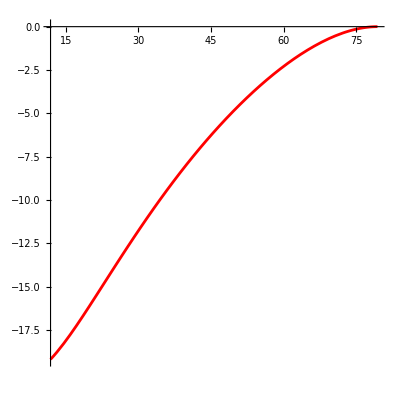

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Kb=20;
γ=0.1;
λ=Sqrt[Kb/γ];
Lc=Rdome*Sin[αB];
RdomeB=Rdome/Lc;
λB=λ/Lc;
fVal=-2;
sbB=5λB;

pψfBs=1.2885597638694775;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-2,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.32933467160871177;
h0Bs=-1.6205586013431466;

sols=FindRoot[shoot[prfBi,pψfBi,h0Bi,fVal]=={0,0,0},{prfBi,prfBs},{pψfBi,pψfBs},{h0Bi,0}];
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;
h0Bs=h0Bi/.sols;
dummy=Evaluate[shoot[prfBs,pψfBs,h0Bs,fVal]];
Print[dummy[[1]]," ",dummy[[2]]," ",dummy[[3]]];

ndsol=SolveShapeEqs[prfBs,pψfBs,h0Bs,fVal];
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
hff[s_]=First[hfB[s]/.ndsol];
Print["pψfBs=",pψfBs," prfBs=", prfBs," h0Bs=",h0Bs]
en=Kb π rff[s] ((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2 (1-Cos[ψff[s]]));
G=NIntegrate[en,{s,s0B,sbB}];
Print[G];
p1=ParametricPlot[{rff[s]*Lc,hff[s]*Lc},{s,s0B,sbB},PlotRange->Full,AspectRatio->1,PlotStyle->Red]
```

```mathematica
pψfBs=-1.0467026200790148;(*Rp=R0,γ=0.7 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.17529148229951277;
h0Bs=-0.1062406995115157;
```

```mathematica
pN=0.1*(π*Kb*(1/Lc)*1.38*(10^-23)*300*10^21);
Print[N[pN]]
```

2.19604

### Asymptotically planar membrane

#### Sweep over F

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Kb=20;
γ=0.1;
λ=Sqrt[Kb/γ];
Lc=Rdome*Sin[αB];
RdomeB=Rdome/Lc;
λB=λ/Lc;
sbB=5λB;
Clear[fVal];(*Dimensionless. Multiply with π Kb/Lc to dimensionalize.*)

(*pψfBs=-0.00145471;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.00037026;
h0Bs=-12.63564442/Lc;(*nm*)*)
(*pψfBs=0;(*Rp=flat,γ=0.0001 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=0;
h0Bs=0;(*nm*)*)
(*pψfBs=-0.3812887632793089;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0.1,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.0948423329164194;
h0Bs=97.48716271712598;*)
(*pψfBs=-0.641120184192086;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0.2,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.10709709140407933;
h0Bs=163.54041271025903;*)
(*pψfBs=-0.3855112493909752;(*Rp=flat,γ=0.0001 Subscript[k, B] T/nm^2,F=0.1,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.011753557341027713;
h0Bs=98.53085749858856;*)
(*pψfBs=-0.31577279108615824;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.05939424551895379;
h0Bs=-0.2263338507279659;*)
(*pψfBs=-5.468977238074078;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=6,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-4.984663265488996;
h0Bs=4.013585601322582;*)
(*pψfBs=-5.605380623086625;(*Rp=flat,γ=0.1 Subscript[k, B] T/nm^2,F=6,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-5.093862419764596;
h0Bs=4.397251236128523;*)
(*pψfBs=-0.49195631529298856;(*Rp=R0,γ=0.2 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.08854573587746278;
h0Bs=-0.17560147256092926;*)
(*pψfBs=-0.6319117556169822;(*Rp=R0,γ=0.3 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.11096302791251;
h0Bs=-0.15012434111563586;*)
(*pψfBs=-0.6696321359212323;(*Rp=R0,γ=0.33 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.1169253835635003;
h0Bs=-0.14456934146241454;*)
(*pψfBs=-0.8590455769052804;(*Rp=R0,γ=0.5 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.1464830424631278;
h0Bs=-0.12221458998210592;*)
(*pψfBs=-1.0467026200790148;(*Rp=R0,γ=0.7 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.17529148229951277;
h0Bs=-0.1062406995115157;*)
(*pψfBs=-0.038041686808686366;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0.01,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.008371596704688304;
h0Bs=8.09892801685981;*)
pψfBs=-0.31577279108615824;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.05939424551895379;
h0Bs=-0.2263338507279659;

Timing[data0=Reap[For[fVal=0,fVal>=-2,fVal=fVal-0.02,
sols=FindRoot[shoot[prfBi,pψfBi,h0Bi,fVal]=={0,0,0},{prfBi,prfBs},{pψfBi,pψfBs},{h0Bi,h0Bs},Method->{"Newton","StepControl"->"LineSearch"},MaxIterations->1000];

pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;
h0Bs=h0Bi/.sols;

dummy=Evaluate[shoot[prfBs,pψfBs,h0Bs,fVal]];
Print["F=",fVal," β=",dummy[[1]]," prfB[sbB]=",dummy[[2]]," h0B[sbB]=",dummy[[3]]];

(*Re-run NDSolve with the converged roots to extract the full profile*)
ndsol=SolveShapeEqs[prfBs,pψfBs,h0Bs,fVal];
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
hff[s_]=First[hfB[s]/.ndsol];

(*Energy Integrand*)
en=Kb π rff[s] ((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2 (1-Cos[ψff[s]]));
Gfootprint=NIntegrate[en,{s,s0B,sbB}];
Gtether=-π Kb fVal h0Bs;
G=Gfootprint+Gtether;
Sow[{fVal,G}];
]
];
]
data=data0[[2]][[1]];
(*Check F=0.0216, F=0.0777 for Rp=Open, MaxIter->100, γ=0.0001*)
(*Check F=0.2129, F=0.2184, F=0.2186. NDSolve fails from F=0.2231 (β=0.0115145) for Rp=R0, MaxIter->100, from F=0.2252 (β=0.00118904) γ=0.0001*)
(*Check F=6.67-6.68 for γ=0.1, Rp=R0*)
(*Check F=15.28-15.32, F=-15.04 for γ=0.2, Rp=R0*)
(*Check F=22.7-24.4, F=-21.92- for γ=0.3, Rp=R0*)
(*Check F=22.5- for γ=0.3, Rp=flat*)
(*Check F=29.38-29.62, -24.26- for γ=0.33, Rp=flat*)
(*Check F=0.2293 for γ=0.0001, F=-15.19 for γ=0.2, Rp=flat*)
```

{11.7344,Null}

```mathematica
Print["pψfBs=",pψfBs,"\nprfBs=",prfBs,"\nh0Bs=",h0Bs]
```

pψfBs=1.28856
prfBs=-0.329335
h0Bs=-1.62056

```mathematica
pψfBs=1.2885597638694775;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=-2,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.32933467160871177;
h0Bs=-1.6205586013431466;
```

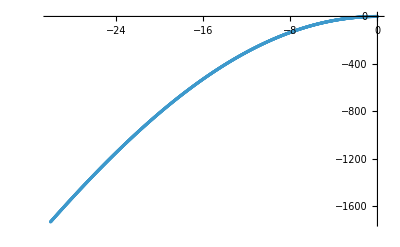

```mathematica
ListPlot[data]
```

```mathematica
Export["F0to-30_vs_Gfootprint_Rpflat_sb5lambda_gamma0.7_beta0_hb0.csv",data]
```

F0to-30_vs_Gfootprint_Rpflat_sb5lambda_gamma0.7_beta0_hb0.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["F0to-0.224_vs_Gfootprint_Rpflat_sb5lambda_gamma0.0001_beta0_hb0.csv"]]]
```

#### Sweep over γ (fixed arclength)

```mathematica
Rdome=41.82077878168754 ;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Kb=20;
Clear[γ];
λ=Sqrt[Kb/γ];
Lc=Rdome*Sin[αB];
RdomeB=Rdome/Lc;
λB=λ/Lc;
sbB=5λB;
fVal=0.2;(*Dimensionless. Multiply with π Kb/Lc to dimensionalize*)

(*pψfBs=-0.00145471;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.00037026;
h0Bs=-12.63564442/Lc;(*nm*)*)
(*pψfBs=0;(*Rp=flat,γ=0.0001 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=0;
h0Bs=0;(*nm*)*)
(*pψfBs=-0.3855112493909752;(*Rp=flat,γ=0.0001 Subscript[k, B] T/nm^2,F=0.1,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.011753557341027713;
h0Bs=98.53085749858856;*)
(*pψfBs=-0.3812887632793089;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0.1,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.0948423329164194;
h0Bs=97.48716271712598;*)
(*pψfBs=-0.641120184192086;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0.2,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.10709709140407933;
h0Bs=163.54041271025903;*)
(*pψfBs=-0.31577279108615824;(*Rp=R0,γ=0.1 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.05939424551895379;
h0Bs=-0.2263338507279659;*)
(*pψfBs=-0.49195631529298856;(*Rp=R0,γ=0.2 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.08854573587746278;
h0Bs=-0.17560147256092926;*)
(*pψfBs=-0.6319117556169822;(*Rp=R0,γ=0.3 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.11096302791251;
h0Bs=-0.15012434111563586;*)
(*pψfBs=-0.6696321359212323;(*Rp=R0,γ=0.33 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.1169253835635003;
h0Bs=-0.14456934146241454;*)
(*pψfBs=-0.8590455769052804;(*Rp=R0,γ=0.5 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.1464830424631278;
h0Bs=-0.12221458998210592;*)
(*pψfBs=-0.038041686808686366;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0.01,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.008371596704688304;
h0Bs=8.09892801685981;*)
(*pψfBs=-0.037749885956421585;(*Rp=flat,γ=0.0001 Subscript[k, B] T/nm^2,F=0.01,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.00013401319961866653;
h0Bs=9.167489741652258;*)

pψfBs=-0.641120184192086;(*Rp=R0,γ=0.0001 Subscript[k, B] T/nm^2,F=0.2,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.10709709140407933;
h0Bs=163.54041271025903;

Timing[data0=Reap[For[γ=0.0001,γ<=1.0001,γ=γ+0.000001,
sols=FindRoot[shoot[prfBi,pψfBi,h0Bi,fVal]=={0,0,0},{prfBi,prfBs},{pψfBi,pψfBs},{h0Bi,h0Bs},Method->{"Newton","StepControl"->"LineSearch"},MaxIterations->1000];

pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;
h0Bs=h0Bi/.sols;

dummy=Evaluate[shoot[prfBs,pψfBs,h0Bs,fVal]];
Print["γ=",γ," β=",dummy[[1]]," prfB[sbB]=",dummy[[2]]," h0B[sbB]=",dummy[[3]]];

(*Re-run NDSolve with the converged roots to extract the full profile*)
ndsol=SolveShapeEqs[prfBs,pψfBs,h0Bs,fVal];
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
hff[s_]=First[hfB[s]/.ndsol];

(*Energy Integrand*)
en=Kb π rff[s] ((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2 (1-Cos[ψff[s]]));
Gfootprint=NIntegrate[en,{s,s0B,sbB}];
Gtether=-π Kb fVal h0Bs;
G=Gfootprint+Gtether;
Sow[{γ,G}];
]
];
]
data=data0[[2]][[1]];
```

Part::partd: Part specification data0⟦2⟧ is longer than depth of object.

```mathematica
Print["pψfBs=", pψfBs,"\nprfBs=",prfBs,"\nh0Bs=",h0Bs];
```

pψfBs=-1.0467
prfBs=-0.175291
h0Bs=-0.106241

```mathematica
pψfBs=-1.0467026200789962;(*Rp=R0,γ=0.7 Subscript[k, B] T/nm^2,F=0,β=0,sb=5λ,Lc=Rdome Sin[αB]*)
prfBs=-0.17529148229950897;
h0Bs=-0.10624069951151706;
```

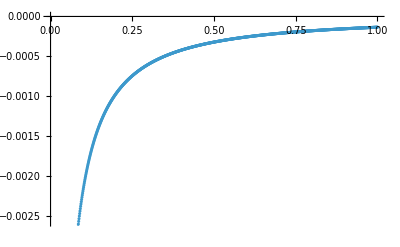

```mathematica
ListPlot[data]
```

```mathematica
Export["gamma0.0001to1.0001_vs_Gfootprint_Rpflat_sb5lambda_F0.01_beta0_hb0.csv",data]
```

gamma0.0001to1.0001_vs_Gfootprint_Rpflat_sb5lambda_F0.01_beta0_hb0.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma0.0001to1.0001_vs_Gfootprint_Rpflat_sb5lambda_F0.01_beta0_hb0.csv"]]]
```

# Monge solutions

```mathematica
ClearAll["Global`*"];

(* =========================================================================*)
(*1. CORE BVP SOLVER*)
(*Computes the energy GM and displacement h(r0) for a specific state*)
(* =========================================================================*)
ComputeFootprint[r0_,a_,rb_,b_,γ_,Fforce_,Kb_]:=Module[{λ,c2,c3,c4,eq1,eq2,sol,c3Val,c4Val,nabla2h0,nabla2hb,h0,GM, GT},
(*Characteristic decay length*)
λ=Sqrt[Kb/γ];
(*Constant c2 is rigidly fixed by the tether force and tension*)
c2=-Fforce/(2 π γ);
(*Slope boundary conditions to find c3 and c4*)(*Note:BesselI'[0,z]=BesselI[1,z] and BesselK'[0,z]=-BesselK[1,z]*)
eq1=c3*BesselI[1,r0/λ]/λ-c4*BesselK[1,r0/λ]/λ==a-c2/r0;
eq2=c3*BesselI[1,rb/λ]/λ-c4*BesselK[1,rb/λ]/λ==b-c2/rb;
sol=Quiet@Solve[{eq1,eq2},{c3,c4}];
If[Length[sol]==0,Return[$Failed]];
c3Val=c3/. sol[[1]];
c4Val=c4/. sol[[1]];
(*Evaluate Laplacians at the boundaries*)(*Note:nabla^2(c2 Log[r])=0,so only Bessel terms remain*)
nabla2h0=(c3Val*BesselI[0,r0/λ]+c4Val*BesselK[0,r0/λ])/λ^2;
nabla2hb=(c3Val*BesselI[0,rb/λ]+c4Val*BesselK[0,rb/λ])/λ^2;
(*Calculate height at Piezo boundary h(r0), utilizing pinning condition h(rb)=0*)
h0=c2*Log[r0/rb]+c3Val*(BesselI[0,r0/λ]-BesselI[0,rb/λ])+c4Val*(BesselK[0,r0/λ]-BesselK[0,rb/λ]);
(*Exact Analytical Bending Energy GM*)
GM=π Kb (rb*b*nabla2hb-r0*a*nabla2h0)+1/2 Fforce*h0;
GT=-Fforce*h0;
<|"GM"->GM,"GT"->GT,"h0"->h0,"c2"->c2,"c3"->c3Val,"c4"->c4Val|>
]

(* =========================================================================*)
(*2. GATING ENERGY CALCULATOR*)
(*Evaluates ΔG=GM_op-GM_cl-F*h_op+F*h_cl*)
(* =========================================================================*)
ComputeGatingEnergy[r0op_,aop_,r0cl_,acl_,rb_,b_,γ_,Fforce_,Kb_]:=Module[{resOp,resCl,dGM, dGT, dGf},
resOp=ComputeFootprint[r0op,aop,rb,b,γ,Fforce,Kb];
resCl=ComputeFootprint[r0cl,acl,rb,b,γ,Fforce,Kb];
If[resOp===$Failed||resCl===$Failed,Return[$Failed]];
(*Total Gating Energy Difference*)
dGM=resOp["GM"]-resCl["GM"];
dGT=resOp["GT"]-resCl["GT"];(*-Fforce*resOp["h0"]+Fforce*resCl["h0"];*)
dGf=dGM+dGT;
<|"dGM"->dGM,"dGT"->dGT,"dGf"->dGf|>
]

(* =========================================================================*)
(*3. HELPER:PIEZO CAP GEOMETRY TO BOUNDARY CONDITIONS*)
(*Converts Cap Area and Radius of Curvature (Rp) into r0 and slope a*)
(* =========================================================================*)
GetBoundaryParams[Area_,Rp_]:=Module[{cosAlpha,alpha,r0,a},
If[Rp===∞,(*Open state:Flat disc*)
r0=Sqrt[Area/π];
a=0;
<|"r0"->r0,"a"->a|>,
(*Closed state:Spherical cap*)
cosAlpha=1-Area/(2 π Rp^2);
alpha=ArcCos[cosAlpha];
r0=Rp*Sin[alpha];
a=Tan[alpha];
<|"r0"->r0,"a"->a|>
]
]

(* =========================================================================*)
(*4. EXECUTION WRAPPER& PLOTTING*)
(* =========================================================================*)
Kb=20.0;
AreaCap=450.0;
RpClosed=41.82077878168754;
RpOpen=∞;

paramCl=GetBoundaryParams[AreaCap,RpClosed];
paramOp=GetBoundaryParams[AreaCap,RpOpen];

rbFixed=200.0;
bSlope=0.0;

gammaList={0.0001,0.001,0.01,0.1,0.2,0.3,0.33,0.5,0.6,0.7,0.8,1};
pNtoKBTnm=1.0/4.142;

(*4a.Data Generation:Extract scalars from the Associations*)
rawData=Table[
Table[
Module[{Fforce=FpN*pNtoKBTnm,resOp,resCl,resGating},
resOp=ComputeFootprint[paramOp["r0"],paramOp["a"],rbFixed,bSlope,γ,Fforce,Kb];
resCl=ComputeFootprint[paramCl["r0"],paramCl["a"],rbFixed,bSlope,γ,Fforce,Kb];
resGating=ComputeGatingEnergy[paramOp["r0"],paramOp["a"],paramCl["r0"],paramCl["a"],rbFixed,bSlope,γ,Fforce,Kb];
(*Return a flat list of scalars for this FpN step*)
{FpN,resOp["GM"],resOp["GT"],resCl["GM"],resCl["GT"],resGating["dGM"],resGating["dGT"],resGating["dGf"]}
],
{FpN,-50,50,0.1}
],
{γ,gammaList}
];

(*4b.Data Formatting for Plots:Extract {FpN,Value} pairs*)
dataDGM=Map[{#[[1]],#[[6]]}&,rawData,{2}];
dataDGT=Map[{#[[1]],#[[7]]}&,rawData,{2}];
dataDGF=Map[{#[[1]],#[[8]]}&,rawData,{2}];

(*4c.Generate the Three-Panel Plot*)
opts={PlotRange->{{-50,50},All},Frame->True,BaseStyle->{FontFamily->"Times",FontSize->14},PlotStyle->AbsoluteThickness[2],ImageSize->350};

myLegend=LineLegend[StringForm["γ = `` \!\(\*SubscriptBox[\(k\), \(B\)]\)T/\!\(\*SuperscriptBox[\(nm\), \(2\)]\)",#]&/@gammaList];

plotGM=ListLinePlot[dataDGM,FrameLabel->{"F (pN)","\!\(ΔG_M\) (\!\(\*SubscriptBox[\(k\), \(B\)]\)T)"},Evaluate@opts];
plotGT=ListLinePlot[dataDGT,FrameLabel->{"F (pN)","\!\(ΔG_T\) (\!\(\*SubscriptBox[\(k\), \(B\)]\)T)"},Evaluate@opts];
plotGF=ListLinePlot[dataDGF,FrameLabel->{"F (pN)","\!\(Δ(G_M+G_T)\) (\!\(\*SubscriptBox[\(k\), \(B\)]\)T)"},PlotLegends->myLegend,Evaluate@opts];

GraphicsRow[{plotGM,plotGT,plotGF},ImageSize->1300]


(* =========================================================================*)
(*5. DATA EXPORT FOR MATPLOTLIB*)
(* =========================================================================*)
Do[γVal=gammaList[[i]];
gammaData=rawData[[i]];
(*Export {F,GM_open,GM_closed}*)
csv1=Prepend[Map[{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]}&,gammaData],{"F_pN","GM_open","GT_open","GM_closed","GT_closed"}];
Export["GM_GT_Open_Closed_vs_F(pN)_b=0_rb=200nm_gamma="<>ToString[γVal]<>".csv",csv1];
,{i,Length[gammaList]}
];
```

-Graphics-

# Symbolic maths for Monge analytics

```mathematica
D1=F/(8 π Kb);
C1=(b rb-a r0-D1 (rb^2-r0^2)-2 D1(rb^2 Log[rb]-r0^2 Log[r0]))/(2(rb^2-r0^2));
B1=(r0 rb (a rb-b r0)+2 D1 r0^2 rb^2 Log[rb/r0])/(rb^2-r0^2);
A1=-B1 Log[rb]-C1 rb^2-D1 rb^2 Log[rb];
h[r_]:=A1+B1 Log[r]+C1 r^2+D1 r^2 Log[r];
```

```mathematica
Gg=4π Kb C1(b rb-ar0)+(F/2)(b rb(Log[rb]+1)-a r0(Log[r0]+1)-h[r0])
```

(2 Kb π (-ar0+b rb) (-a r0+b rb-(F (-r0^2+rb^2))/(8 Kb π)-(F (-r0^2 Log[r0]+rb^2 Log[rb]))/(4 Kb π)))/(-r0^2+rb^2)+1/2 F (-(F r0^2 Log[r0])/(8 Kb π)-a r0 (1+Log[r0])+(F rb^2 Log[rb])/(8 Kb π)+b rb (1+Log[rb])-(r0^2 (-a r0+b rb-(F (-r0^2+rb^2))/(8 Kb π)-(F (-r0^2 Log[r0]+rb^2 Log[rb]))/(4 Kb π)))/(2 (-r0^2+rb^2))+(rb^2 (-a r0+b rb-(F (-r0^2+rb^2))/(8 Kb π)-(F (-r0^2 Log[r0]+rb^2 Log[rb]))/(4 Kb π)))/(2 (-r0^2+rb^2))-(Log[r0] (r0 rb (-b r0+a rb)+(F r0^2 rb^2 Log[rb/r0])/(4 Kb π)))/(-r0^2+rb^2)+(Log[rb] (r0 rb (-b r0+a rb)+(F r0^2 rb^2 Log[rb/r0])/(4 Kb π)))/(-r0^2+rb^2))

```mathematica
Simplify[Gg,rb>r0]
```

1/(32 Kb π (r0^2-rb^2))(-64 a ar0 Kb^2 π^2 r0+8 ar0 F Kb π r0^2-24 a F Kb π r0^3+F^2 r0^4+64 ar0 b Kb^2 π^2 rb+64 a b Kb^2 π^2 r0 rb+16 b F Kb π r0^2 rb-8 ar0 F Kb π rb^2-64 b^2 Kb^2 π^2 rb^2+24 a F Kb π r0 rb^2-2 F^2 r0^2 rb^2-16 b F Kb π rb^3+F^2 rb^4-4 F rb Log[rb] (4 Kb π (-2 b r0^2+ar0 rb+a r0 rb)+F r0^2 rb Log[rb/r0])+4 F r0 Log[r0] (4 Kb π (ar0 r0-a r0^2-2 b r0 rb+2 a rb^2)+F r0 rb^2 Log[rb/r0]))

$Aborted